## Monte Carlo Simulation

Essentially, a Monte Carlo simulation is just a way to figure out what a probability distribution looks like by simulating the random process and visualizing/analyzing the resulting distribution. This is the most general way to figure out what a distribution looks like, it’s essentially fool proof because you’re just simulating the process, and it’s really simple in Mathematica. The only downsides are that you don’t get an analytical formula for the distribution, it can be slow as it requires a lot of samples to yield good results, and the results are subject to randomness, and as such you can never know the “true” answer, you can only get arbitrarily close for large sample sizes.

Doing this in Mathematica is very simple, and we actually saw two examples last week. First, however, I want to explain the two main functions I use to run these simulations

### Table

Table is used to create lists of data in Mathematica. It’s a bit like using a loop, although it’s only one line and it’s more efficient in most cases. You’ve probably seen me use it multiple times throughout the class, and it’s long-overdue that I properly introduce it

```mathematica
(* Here's a simple example which shows how you can use it to make a list that ranges from 1 to 10 with spaces of 0.5 between jumps. In this regard, it is a lot like numpy's linspace() in python*)
imin=1;
imax=10;
Δi=0.5;
Table[i,{i,imin,imax,Δi}]
```

{1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

```mathematica
(* If you don't specify a Δi value, it defaults to 1 *)
imin=1;
imax=10;
Δi=0.5;
Table[i,{i,imin,imax}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
(* You can also return any expression of i, and not just i *)
imin=1;
imax=10;
Δi=0.5;
Table[i^2,{i,imin,imax}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
(* You can also specify the exact value that i will take on by giving it a list instead of a min and max *)
Table[i^2,{i,{10,3,2,π,a,b,c}}]
```

{100,9,4,π^2,a^2,b^2,c^2}

```mathematica
(* Finally, you can also loop over as many variables as you like in what ever manner you like (as lists, ranges, etc) by simply adding another variable. The result will be an n-dimensional array when you specify n-variables *)
matrix=Table[Subscript[M, i,j],{i,1,5},{j,1,10}]
matrix//MatrixForm
```

{{M_(1,1),M_(1,2),M_(1,3),M_(1,4),M_(1,5),M_(1,6),M_(1,7),M_(1,8),M_(1,9),M_(1,10)},{M_(2,1),M_(2,2),M_(2,3),M_(2,4),M_(2,5),M_(2,6),M_(2,7),M_(2,8),M_(2,9),M_(2,10)},{M_(3,1),M_(3,2),M_(3,3),M_(3,4),M_(3,5),M_(3,6),M_(3,7),M_(3,8),M_(3,9),M_(3,10)},{M_(4,1),M_(4,2),M_(4,3),M_(4,4),M_(4,5),M_(4,6),M_(4,7),M_(4,8),M_(4,9),M_(4,10)},{M_(5,1),M_(5,2),M_(5,3),M_(5,4),M_(5,5),M_(5,6),M_(5,7),M_(5,8),M_(5,9),M_(5,10)}}

(M_(1,1) | M_(1,2) | M_(1,3) | M_(1,4) | M_(1,5) | M_(1,6) | M_(1,7) | M_(1,8) | M_(1,9) | M_(1,10)
M_(2,1) | M_(2,2) | M_(2,3) | M_(2,4) | M_(2,5) | M_(2,6) | M_(2,7) | M_(2,8) | M_(2,9) | M_(2,10)
M_(3,1) | M_(3,2) | M_(3,3) | M_(3,4) | M_(3,5) | M_(3,6) | M_(3,7) | M_(3,8) | M_(3,9) | M_(3,10)
M_(4,1) | M_(4,2) | M_(4,3) | M_(4,4) | M_(4,5) | M_(4,6) | M_(4,7) | M_(4,8) | M_(4,9) | M_(4,10)
M_(5,1) | M_(5,2) | M_(5,3) | M_(5,4) | M_(5,5) | M_(5,6) | M_(5,7) | M_(5,8) | M_(5,9) | M_(5,10))

```mathematica
(* Also another useful function to couple this with in some cases is flatten, which can turn these multi-dimensional lists back into 1D lists. I recomend reading the docs for Flatten, it's pretty simple to use *)
Flatten[Table[Subscript[M, i,j],{i,1,5},{j,1,10}],1]
```

{M_(1,1),M_(1,2),M_(1,3),M_(1,4),M_(1,5),M_(1,6),M_(1,7),M_(1,8),M_(1,9),M_(1,10),M_(2,1),M_(2,2),M_(2,3),M_(2,4),M_(2,5),M_(2,6),M_(2,7),M_(2,8),M_(2,9),M_(2,10),M_(3,1),M_(3,2),M_(3,3),M_(3,4),M_(3,5),M_(3,6),M_(3,7),M_(3,8),M_(3,9),M_(3,10),M_(4,1),M_(4,2),M_(4,3),M_(4,4),M_(4,5),M_(4,6),M_(4,7),M_(4,8),M_(4,9),M_(4,10),M_(5,1),M_(5,2),M_(5,3),M_(5,4),M_(5,5),M_(5,6),M_(5,7),M_(5,8),M_(5,9),M_(5,10)}

### RandomVariate

This is the function which does the meat of the Monte Carlo simulation for you. RandomVariate takes a distribution in Mathematica and generates a random number from that distribution. As computers are in-capable of generating truly random numbers, it uses a pseudo-random number generator to do this, whose seed can be set using SeedRandom[]. This way you will get the same results every time you run it after resetting the seed. But the results appear random for an arbitrary seed choice. 

Here we randomly sample a single number from a normal distribution with a mean of 1 and a standard deviation of 0.1

```mathematica
SeedRandom[12341];
RandomVariate[NormalDistribution[1,0.1]]
```

1.10054

On its own, this isn’t too useful. What makes it very useful, however, is that if you pass it a second parameter you can have it generate tons of samples for you at once which you can then plot

Here we generate 10,000 samples and plot them as a histogram

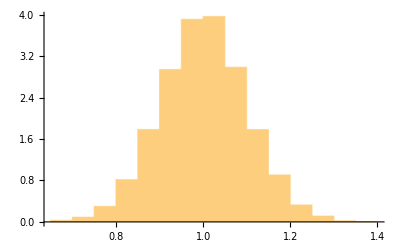

```mathematica
SeedRandom[12341];
samples=RandomVariate[NormalDistribution[1,0.1],10000];

Histogram[samples,Automatic,"PDF"]
```

We can see we get the exact normal distribution we expected with mean 1 and stdev of 0.1

But we can do much more, for instance we can see what the distribution of a transformed variable will look like by transforming all the variable sin our list. When someone says they’re squaring a random variable for instance, this is what they mean. Then mean they’re sampling it from one population and then squaring the result after sampling. Obviously this changes the resulting distribution.

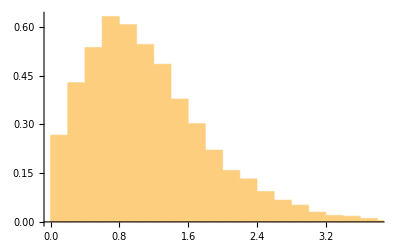

```mathematica
SeedRandom[12341];
samples=#^2&/@RandomVariate[NormalDistribution[1,0.35],10000];
Histogram[samples,Automatic,"PDF"]
```

Here we get a new distribution which is actually the chi-squared distribution with df = 1. This is all the chi-squared distribution is btw, it’s the distribution you get when you sample a value from a normally distributed population and then square it before plotting it. 

Finally, the last thing I want to show you how to simulate is a sampling distribution. Here the idea is we take a sample of a distribution, lets say with a sample size of 35 for instance. And then you want to know how likely you are to get a given mean for your sample. You can simulate this by taking the means of a bunch of samples, each sample you can make with RandomVariate[]. Here’s and example

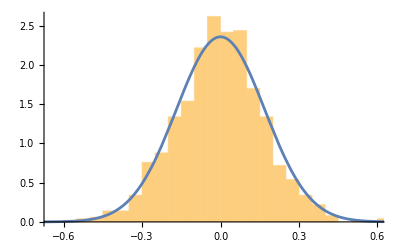

```mathematica
(* Define any distribution you want. Here we make our own, but you could also use a built in one like NormalDistribution[μ,σ] like we saw before*)
SeedRandom[1231];
PopulationDistribution =ProbabilityDistribution[Sqrt[2]/Pi/(1+x^4),{x,-∞,∞}]; 
SampleSize=35;
NumberOfSamples = 1000;
SampleDistData=Table[Mean[RandomVariate[PopulationDistribution,SampleSize]],{i,1,NumberOfSamples}];
Show[{
Histogram[SampleDistData,Automatic,"PDF"],
Plot[PDF[NormalDistribution[0,1/(√35)],x],{x,-1,1}]
}]
```

We can see that despite our original distribution not being normally distributed, our distribution of sample means is. This is the central limit theorem in action, which holds because our sample size of 35 is sufficiently large. But this isn’t really a case where Monte Carlo is too useful, cause we could just use the CLT instead. But what if our sample size was much smaller, like 3 for instance. In that case we get the following distribution instead

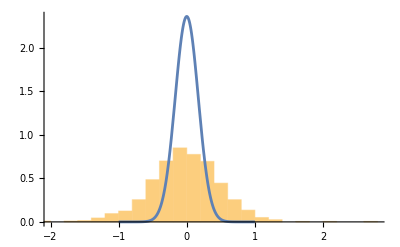

```mathematica
SeedRandom[1231];
PopulationDistribution =ProbabilityDistribution[Sqrt[2]/Pi/(1+x^4),{x,-∞,∞}]; 
SampleSize=3;
NumberOfSamples = 1000;
SampleDistData=Table[Mean[RandomVariate[PopulationDistribution,SampleSize]],{i,1,NumberOfSamples}];
Show[{
Histogram[SampleDistData,Automatic,"PDF"],
Plot[PDF[NormalDistribution[0,1/(√35)],x],{x,-1,1}]
}]
```

Aha, that’s not normal at all, it’s tails are way too thick. And as a result, we could use monte-carlo simulation to understand the true distribution when the CLT just doesn’t cut it. Pretty slick, and hopefully not that hard to do.

## Symbolic Probability

But what if we don’t just want to see the data, what if we want an actual symbolic representation of a PDF? Well, Mathematica can do that too. And to understand how I want to introduce a few more key functions.

### ProbabilityDistribution

This function lets you define your own probability distributions based on any arbitrary function of your choice.

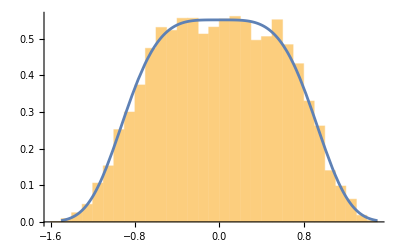

```mathematica
f[x_]:=1/(2 Gamma[5/4])ⅇ^(-x^4)

(* Define based on the PDF of the distribution *)
dist=ProbabilityDistribution[f[x],{x,-∞,∞}];

SeedRandom[12341];
Show[{
Histogram[RandomVariate[dist,10000],Automatic,"PDF"],
Plot[f[x],{x,-1.5,1.5}]
},PlotRange->All]
```

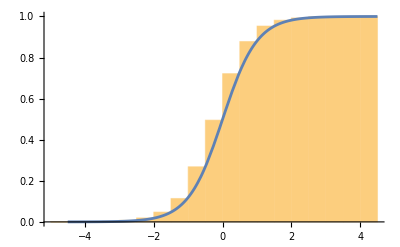

```mathematica
F[x_]:=1/2(1+Tanh[x])

(* Define based on the CDF of the distribution *)
dist=ProbabilityDistribution[{"CDF",F[x]},{x,-∞,∞}];

SeedRandom[12341];
Show[{
Histogram[RandomVariate[dist,10000],Automatic,"CDF"],
Plot[F[x],{x,-4.5,4.5}]
},PlotRange->All]
```

All of these custom distributions can be used wherever any of the built in distributions can be used. 

You can also define them based off of survival functions or hazard functions instead of CDFs or PDFs

NOTE: Even though Mathematica won’t throw an error if you functions are not properly normalized, you must ensure that they are. I’ve noticed that some really weird bugs can occur if you don’t normalize it yourself! Some things like RandomVariate actually seem to work, but symbolic operations which use the distribution will give you the wrong answers if your distribution is not normalized!

For definitions based on the PDF this means the total area of your function on the domain you specify the distribution should be 1
		i.e.	 ∫_xmin^xmax PDF[x]ⅆx=1  

	For definitions based on the CDF the limit of the cdf should approach 1
		i.e.	lim_(x->xmax) CDF[x]=1

### PDF and CDF

If you already have some distribution and you want to grab it’s PDF, or CDF you can simply call PDF or CDF on it and tell it what variable to use (if you give it a number instead of a variable it will return the PDF or CDF evaluated at that variable)

```mathematica
Clear[μ,σ,x]
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
CDF[NormalDistribution[μ,σ],x]
```

1/2 Erfc[(-x+μ)/(√2 σ)]

You can also grab Characteristic Functions too if you know what those are

```mathematica
CharacteristicFunction[NormalDistribution[μ,σ],t]
```

ⅇ^(ⅈ t μ-(t^2 σ^2)/2)

### Probability and NProbability

The probability function in Mathematica does exactly what you might expect, it tells you the probability of things. 

Here’s how you use it, you give it an inequality or similar expression, and you tell it how the variables in that expression are distributed. 

Reminder that you can type the \[Distributed] symbol by typing dist where  represents the escape key so: esc dist esc

Here’s an example to find the probability that a normally distributed variable is within 1 standard deviation of the mean for instance

```mathematica
Clear[μ,σ]
Probability[μ-σ<x<μ+σ,x\[Distributed]NormalDistribution[μ,σ]]
```

Erf[1/(√2)]

And here is the probability that the ratio of two normally distributed variables is greater than some value. By default mathematic tries to do this symbolically which will take forever for complicated situations like this, so we can use NProbability instead to solve this numerically.

```mathematica
NProbability[x/y>2,{x\[Distributed]NormalDistribution[4,1],y\[Distributed]NormalDistribution[3,2]}]
```

0.247006

NOTE: Despite being done numerically, these are different from Monte Carlo Simulations. Mathematica may try to use probability theory to predict the result and just use numerical approximations to compute the integrals needed to get to this answer. You can tell Mathematica to answer the question using a Monte Carlo Simulation in the background. By default Mathematica chooses which method to use, and will usually choose a deterministic method if it can.

```mathematica
NProbability[x/y>2,{x\[Distributed]NormalDistribution[4,1],y\[Distributed]NormalDistribution[3,2]},Method->"NIntegrate"]
NProbability[x/y>2,{x\[Distributed]NormalDistribution[4,1],y\[Distributed]NormalDistribution[3,2]},Method->"MonteCarlo"]
```

0.247006

0.24744

Also for those who are curious this is what Mathematica is doing with NIntegrate in the background in an example like that, it’s probably something like this: https://en.wikipedia.org/wiki/Ratio_distribution, but using numerical integration

### Expectation and NExpectation

Knowing how likely things are to occur is obviously very useful, but in a lot of cases you want to know what the expected value of a certain random variable is. In probability, statistical expectation refers to the average value you would get if you repeated a statistical process an infinite number of times, and is as such referred to as a long-run average 

Finding expected values is very similar to finding probabilities. For instance, if we want the expected value of a normally distributed random variable we could do the following:

```mathematica
Expectation[x,x\[Distributed]NormalDistribution[μ,σ]]
```

μ

We can see that we always get the mean of the distribution, which is expected as the expectation of a random variable is its mean by definition. But what if we wanted to know the expected value for x^2 for instance?

```mathematica
Expectation[x^2,x\[Distributed]NormalDistribution[μ,σ]]
```

μ^2+σ^2

Now we can see the most likely value for the square of a normally distributed random variable is a function of the mean and variance of the distribution which is pretty cool.

And just like with Probability[] we can ask Mathematica to find this numerically instead of symbolically, and we can include expressions of multiple random variables:

```mathematica
NExpectation[(x^2+y^2)^2,{x\[Distributed]NormalDistribution[1,2],y\[Distributed]NormalDistribution[5,2]}]
```

1636.

Or even using custom distributions like we defined above

```mathematica
NExpectation[Cos[x+y],{x\[Distributed]ProbabilityDistribution[1/(2 Gamma[5/4])ⅇ^(-x^4),{x,-∞,∞}],y\[Distributed]ProbabilityDistribution[{"CDF",1/2(1+Tanh[y])},{y,-∞,∞}]}]
```

0.574094

Btw, doing everything that one line of code does  by hand would probably take me about 30 minutes at the very least.

### Finding the standard deviation of distributions

Note, that there is no function like Variance or Skew, etc which work like Expectation. The reason for this, is that you don’t need one as all of these higher moments can be found using the expectation formula. This is because the variance of any distribution can be defined as follows: 

σ_x^2= 𝔼[x^2] - 𝔼[x]^2           ⇔            σ_x=√(𝔼[x^2] - 𝔼[x]^2)

Where 𝔼 means “expected value of” and σ_x is the standard deviation of x, and σ_x^2 is the variance of x

Note that this formula comes directly from the definition of the standard deviation, and just simplifies down to this form. Perhaps try doing this for yourself if you’re curious. You can even have Mathematica do it for you symbolically.

Anyway, we can also verify this formula using normal distributions like this:

```mathematica
Clear[x,μ,σ]
Expectation[x^2,x\[Distributed]NormalDistribution[μ,σ]]-Expectation[x,x\[Distributed]NormalDistribution[μ,σ]]^2
```

σ^2

And now let’s find the variance of the example we saw before

```mathematica
m1=NExpectation[Cos[x+y],{x\[Distributed]ProbabilityDistribution[1/(2 Gamma[5/4])ⅇ^(-x^4),{x,-∞,∞}],y\[Distributed]ProbabilityDistribution[{"CDF",1/2(1+Tanh[y])},{y,-∞,∞}]}]
m2=NExpectation[Cos[x+y]^2,{x\[Distributed]ProbabilityDistribution[1/(2 Gamma[5/4])ⅇ^(-x^4),{x,-∞,∞}],y\[Distributed]ProbabilityDistribution[{"CDF",1/2(1+Tanh[y])},{y,-∞,∞}]}]
σ=√(m2-m1^2)
```

0.574094

0.56393

0.484093

And perhaps it’s worth reminding ourselves what this example actually represents. 

Lets say we have some process X which can gives us random values. We know that as we sample more and more values from X, the resulting histogram starts to look more and more like the function 1/(2 Gamma[5/4])ⅇ^(-x^4)

We also have some process Y which can give us random values. And when we sample more and more values from Y, and plot a cumulative histogram of their values, it looks like the function 1/2(1+Tanh[y])

Then, if we were to take a random value from X and a random value from Y, and put both of these through the function Cos(x+y) we could expect to see a new distribution. If you sampled this distribution (by repeating this process of sampling from X and Y and putting them through cos(x+y)) and took the mean of that distribution you would get the value m1 = 0.574094. If you instead took every value you sampled and squared it and then took the mean of the squared values, you would get m2 = 0.56393, and if you finally took the standard deviation of the list of samples, you would get σ=√(m2-m1^2)

### Joint Probability

In all of the above examples, it was assumed that any variables used were independent of each-other. For instance in the example we just saw, we assume that the value we get for x does not influence the value we get for y. But what if this isn’t the case? What if x and y represent the values two certain probes give us. Maybe x represents the time it takes you to drive to work each day, and y represents the time it takes your friend to drive in. Obviously x won’t always be the same as y, but if x increases, we expect y to also increase and vice versa (assuming you don’t drive from completely different directions, and even then they could still be correlated due to how traffic works)

In such an example, you would represent x and y with a joint probability distribution. In other-words you would have one function f[x,y] not two independent functions f[x] and f[y].  

Note that for independent processes f[x,y]=f[x]f[y] but for something like the daily commute example f[x,y] ≠ f[x]f[y]

To represent such a distribution in Mathematica, we can once again use ProbabilityDistribution

```mathematica
dist = ProbabilityDistribution[ⅇ^(1/2 (-((-1+x) (2/5 (-1+x)+1/5 (-3+y)))-(1/5 (-1+x)+3/5 (-3+y)) (-3+y)))/(2 √5 π),{x,-∞,∞},{y,-∞,∞}];
(* Note that here the double integral of the function must always be 1 *)
∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(1/2 (-((-1+x) (2/5 (-1+x)+1/5 (-3+y)))-(1/5 (-1+x)+3/5 (-3+y)) (-3+y)))/(2 √5 π)ⅆxⅆy
```

1

After declaring a distribution like this, we can use it however we want. I recommend using Numerical functions though, because these multivariate computations get really complex really fast.

```mathematica
NProbability[x>y,{x,y}\[Distributed]dist]
NExpectation[x^2+y^2,{x,y}\[Distributed]dist]
```

0.224846

15.

### Conditional Probability

What if we want to ask a question like: 

“What is the value of x given y is....”

This is a conditional probability problem and Mathematica can handle using the \[Conditioned] symbol which is typed as cond (esc cond esc) 

Here are some examples

```mathematica
dist = ProbabilityDistribution[ⅇ^(1/2 (-((-1+x) (2/5 (-1+x)+1/5 (-3+y)))-(1/5 (-1+x)+3/5 (-3+y)) (-3+y)))/(2 √5 π),{x,-∞,∞},{y,-∞,∞}];
NProbability[0<x<3\[Conditioned]y==2,{x,y}\[Distributed]dist]
NExpectation[x\[Conditioned]y==2,{x,y}\[Distributed]dist]

NExpectation[Sin[x]\[Conditioned](-π<x<π),x\[Distributed]NormalDistribution[1,3]]
```

0.657218

1.5

0.105959

## For more, check out this page: Probability & Statistics